```mathematica
L=1
f[x_]:=Abs[x^(1/3)]
```

1

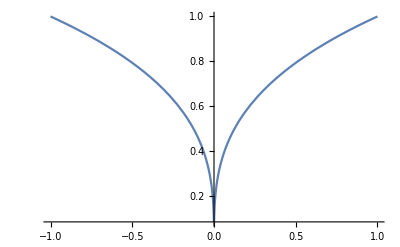

```mathematica
Plot[f[x],{x,-1,1}]
```

```mathematica
g[x_]=Piecewise[{{(1/3)*(-x)^(-2/3),-L<x<0},{(1/3)*(x)^(-2/3),0<x<L}}]
```

Piecewise[{{1/(3 (-x)^(2/3)), -1<x<0}, {1/(3 x^(2/3)), 0<x<1}, {0, True}}]

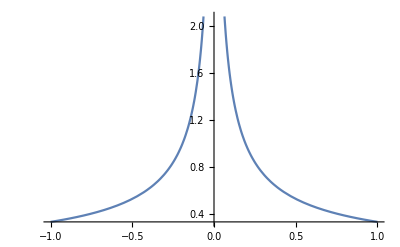

```mathematica
Plot[g[x],{x,-L,L}]
```

```mathematica
h[x_]=Piecewise[{{1,0<x<1},{-x,-1<x<0}}]
```

Piecewise[{{1, 0<x<1}, {-x, -1<x<0}, {0, True}}]

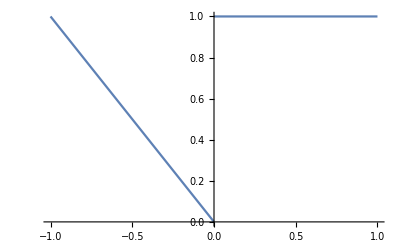

```mathematica
Plot[h[x],{x,-1,1}]
```

```mathematica
i[x_]=Piecewise[{{0,0<x<1},{-1,-1<x<0}}]
```

Piecewise[{{0, 0<x<1}, {-1, -1<x<0}, {0, True}}]

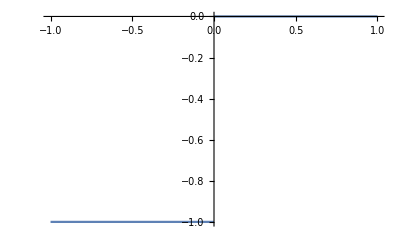

```mathematica
Plot[i[x],{x,-1,1}]
```

```mathematica
j[x_]=Piecewise[{{Tan[1/x],0<x<1},{-1,-1<x<0}}]
```

Piecewise[{{Tan[1/x], 0<x<1}, {-1, -1<x<0}, {0, True}}]

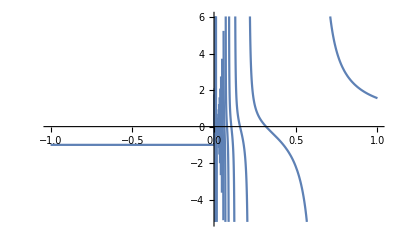

```mathematica
Plot[j[x],{x,-1,1}]
```

```mathematica
k[x_]=Piecewise[{{((Sec[1/x])^2)*(-1/(x^2)),0<x<1},{0,-1<x<0}}]
```

Piecewise[{{-Sec[1/x]^2/x^2, 0<x<1}, {0, True}}]

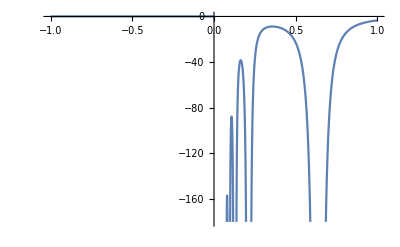

```mathematica
Plot[k[x],{x,-1,1}]
```